Mathematical Techniques in Evolution and Ecology

# Numerical and graphical techniques

Based on Chapter 4 in Otto and Day (2007)

Spring Quarter 2015
Simon Aeschbacher
saeschbacher@ucdavis.edu

## Outline

### Goal

To describe numerical and graphical techniques for exploring a model’s behaviour

### Concepts

Initial conditions

Variable over time plots

General solution

Variable versus variable plots

### See OD2007:

Phase-plane diagrams

Vector-field plots

Null clines

## Motivation

In the following units, we will explor analytical techniques to study mathematical models. Before doing so, in this unit we learn how we can get a feel for a model’s behaviour through numerical and graphical techniques.

Basic idea: Specify numerical values for all of the parameters and for the initial values of each variable, and then use the model’s equations to predict what happens over time

Downside: Not well suited for understanding the model in general terms

Three main types of graphs

Variable(s) as a function of time: Illustrate the dynamics for a given set of parameters

(Change in) a variable as a function of the variable itself: Illustrate conditions under which a variable grows or shrinks

One variable as a function of another variable: Illustrate the effect of interactions

## Plots of variables over time

### Initial conditions

Initial conditions, also called “starting conditions” are the numerical values of every variable at the initial time point. Often, the qualitative and quantitative behaviour of the dynamics depends on the initial conditions.

### Variabe over time plots

Illustrate the behaviour of the variable of interest (vertical axis) as a function of time (horizontal axis).

For discrete-time models, the recursion equations allow us to plot successive values of the variables, given the initial conditions

Sometimes, a general solution can be found. A general solution is an equation that gives the value of a variable at any future point in time as a function of the parameters, the initial conditions, and the time.

#### Exercises

(a) Starting from the discrete-time recursion equation for the exponential growth model, n(t+1)=R n(t), derive the general solution, i.e. express n(t) as a function of R, n(0), and t.

(b) Tind the explicit solution for the continuous-time version, starting from the differential equation ⅆn/ⅆt=r n(t), and making an educated guess based on the general solution in discrete time obtained above.

#### Example: Discrete-time dynamics of the exponential growth model

The dots in the plots below have been produced by iterating the discrete-time recursion equations. The curves were obtained from the explicit solution. For details, see part (a) of the Exercise above.

```mathematica
expGrowthPlot1
```

-Graphics-

```mathematica
expGrowthPlot2
```

-Graphics-

#### Example: Logistic growth model

For most models, it is not so simple to obtain a general solution as it was for the exponential growth model above. Trying to iterate the recursion equation for the logistic growth model becomes nasty pretty soon:

n (t+1)=n(t)+ r n( t) (1-(n(t))/K).

However, we can use a calculator (e.g. Mathematica, Maple, Matlab, R) to numerically iterate the recursion.

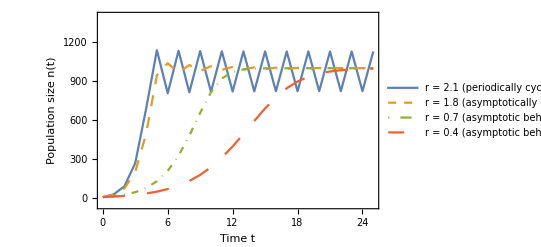

```mathematica
logisticGrowthPlotRec1
```

n (t+1)=n(t)+ r n( t) (1-(n(t))/K).

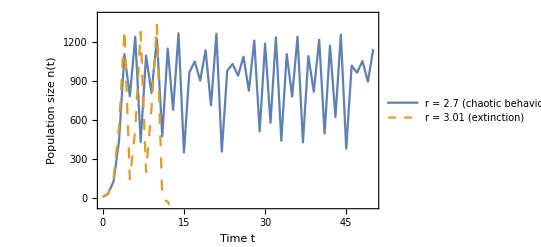

```mathematica
logisticGrowthPlotRec2
```

#### Chaos

Superficially, chaotic dynamics (see example above, with r=2.7) appear to be erratic and random, but they are, in fact, entirely predictable and deterministic. If we know the values of the parameters and variables, we can predict the population size at any future time simply by iteration of the recursion equation.

On the other hand, chaotic dynamics imply that the future state of the system will be sensitive to imprecision in the calculations, e.g. due to rounding errors.

There is a continued debate about the importance of chaos (and periodic cyclies) in biology (e.g. Dennis et al. 2001, Ecol. Monogr. 71:277–303; Hastings et al. 1993, Ecology 72:896–903; Turchin and Ellner 2000, Ecology 81:3099–3116).

Do we see chaotic behaviour in the continuous-time version, too?

#### Discretising a differential equation: Euler’s Method

In a later unit, we will learn how to find the general solution from the differential equation of the logistic growth model, which we could then plot. Here, we instead analyse the differential equation numerically. This can be a useful technique if a general solution cannot be found.

Let us start from the definition of the differential:

ⅆn/ⅆt:=lim_(Δt→0) (n(t+Δt) -n(t))/Δt.

In practice, we cannot let Δt go to infinity in our calculations. However, we can choose a very small Δt and then approximate the differential as

ⅆn/ⅆt≈[(n(t+Δt)-n(t))/Δt]_(for Δt very small).

Hence,

n(t+Δt)≈n(t)+Δt ⅆn/ⅆt

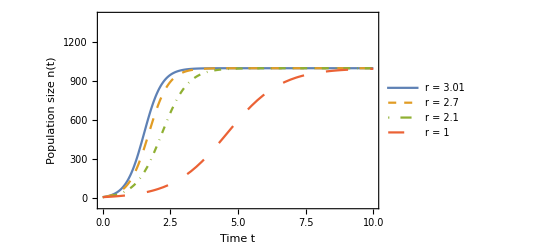

```mathematica
logisticGrowthContPlot
```

We see no cyclic or chaotic behaviour in continuos time! Why is this so?

Comparing the discrete-time model (recursion equation) with the discretised continuous-time model, we see that the two agree well as long as r is small:

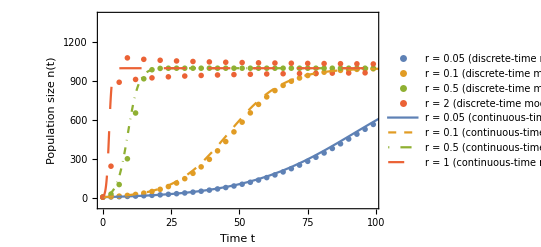

```mathematica
logisticGrowthCompareContDiscPlot
```

Hence, results obtained with the continuous-time approximation are robust w.r.t. to the discrete-time version as long as r is not too large.

### Example: Models of natural selection

In the logistic growth model the agreement between the discrete-time and continuous-time version was sensitive to the choices of parameter values (and hence to underlying assumptions). In contrast, the haploid and diploid models of natural selection display very similar dynamics in discrete and continuous time (cf. Fig. 4.6 in OD2007).

However, the behaviour of models of selection is sensitive to the ordering of fitnesses, i.e. to the relative magnitude of the fitnesses:

Overdominance, or heterozygote advantage

W_AA<W_Aa>W_aa

Directional selection

W_AA>W_Aa>W_aa

W_AA<W_Aa<W_aa

Underdominance, or heterozygote disadvantage

W_AA>W_Aa<W_aa

#### Overdominance (heterozygote advantage)

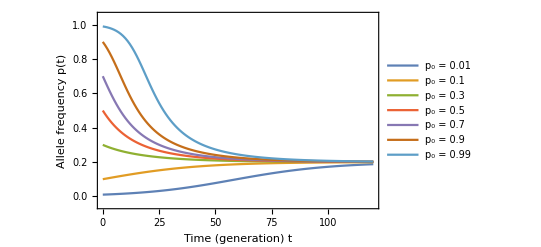

```mathematica
diplSelOverdomPlot
```

#### Directional selection in favour of allele A

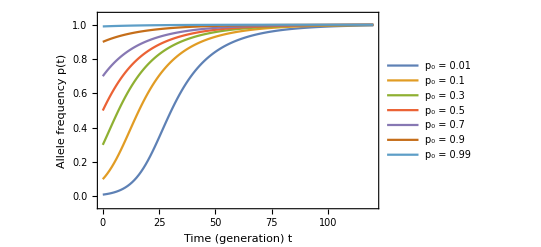

```mathematica
diplSelDirectPlot
```

#### Underdominance (heterozygote disadvantage)

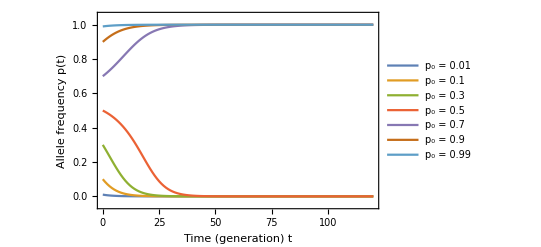

```mathematica
diplSelUnderdomPlot
```

## Plots of variables as a function of themselves

Variable-versus-variable plots illustrate the future state or change of a variable (vertical axis) versus the current state of the variable (horizontal axis):

"function of n(t+1) ~ function of n(t)"

Such plots help us understand the dynamics of one-variable models, as they illustrate how the direction of change depends on the current state.

### Value of a variable at time t+1 versus time t

We plot the recursion equation as a function of the variable itself:

n(t+1) ~ n(t)

#### Example 1: Haploid model of selection

We plot the recursion equation for p(t),

p(t+1)=(W_A p(t))/(W_A p(t)+W_a(1-p(t)))

as a function of p(t) itself.

Looking at the following two plots:

What does the diagonal line represent?

What does it mean if the curve crosses the diagonal?

Use the cobwebbing technique to determine how the variable changes over time

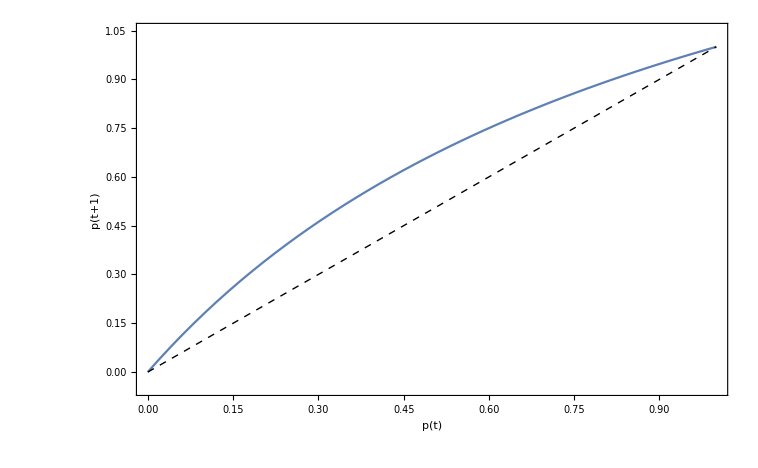

```mathematica
haplSelRecCWPlot[1,0.5]
```

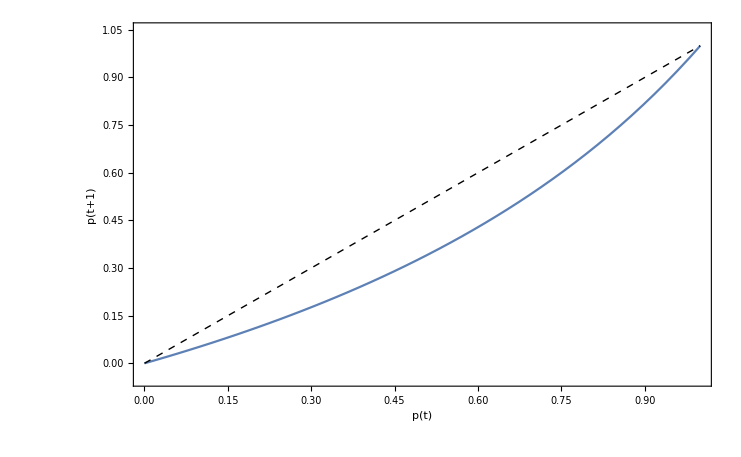

```mathematica
haplSelRecCWPlot[0.5,1]
```

#### Example 2: Diploid model of selection

We plot the recursion equation for p(t),

p(t+1)=(W_AA p(t)+W_Aa(1-p(t)))/(W_AA p^2(t)+2 W_Aa p(t)(1-p(t))+(W_aa(1-p(t)))^2)p(t)

as a function of p(t) itself.

In the following three plots, use the cobwebbing technique to determine the type of the equilibria.

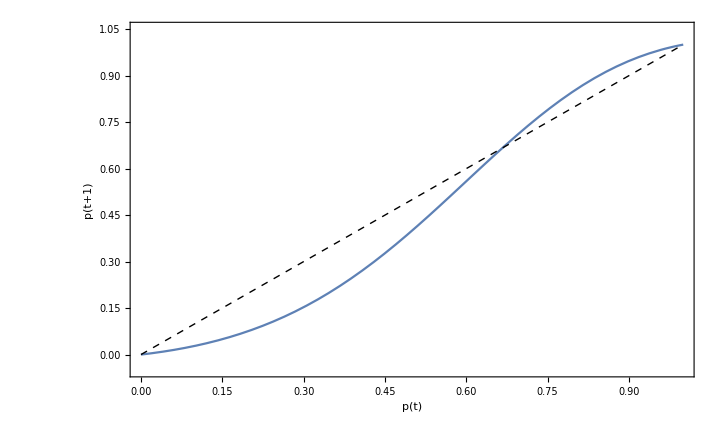

```mathematica
diplSelRecCWPlot[0.6,0.2,1.]
```

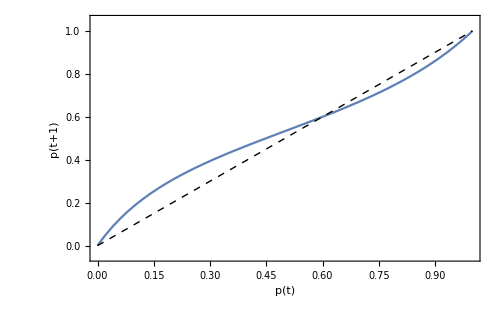

```mathematica
diplSelRecCWPlot[0.6,1,0.4]
```

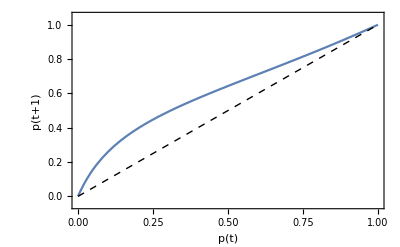

```mathematica
diplSelRecCWPlot[1,0.8,0.2]
```

#### Example 3: Logistic growth model

We plot the recursion equation for n(t),

n(t+1)=n(t)*(1+r-r/K n(t))=n(t)+r n(t)(1-(n(t))/K)

as a function of n(t) itself.

In the following three plots, use the cobwebbing technique to determine the type of the equilibria.

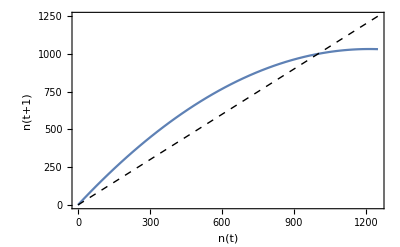

```mathematica
logisticGrowthCWPlot[0.7,1000]
```

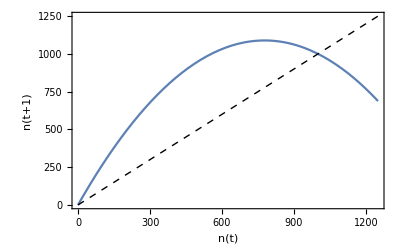

```mathematica
logisticGrowthCWPlot[1.8,1000]
```

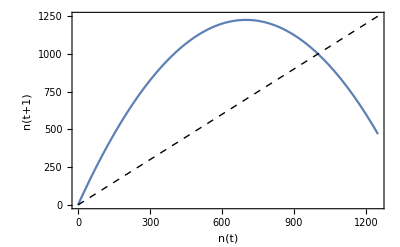

```mathematica
logisticGrowthCWPlot[2.5,1000]
```

#### The slope of the recursion at the equilibrium

Looking at the various plots and cobwebs above, we see that an equilibrium is

locally stable if the slope of the recursion at the equilibrium is <1, and

unstable if the slope of the recursion at the equilibrium is >1.

### Change in a variable versus variable at time t [Go on here]

We plot the difference or the differential equation as a function of the variable itself:

Δn(t) ~ n(t)

(ⅆn(t))/ⅆt ~ n(t)

#### Example: Diploid model of natural selection

Consider the following fitness parametrisation:

W_AA=1+s                    W_Aa=1+h s                    W_aa=1.

We plot the continuous-time differential equation

(ⅆp(t))/ⅆt=s p(1-p) (p+h (1-2 p))

as a function of p(t).

```mathematica
Manipulate[diplSelDotPlot[s,h],{{s,0.2},-0.5,0.5},{{h,0.5},-1,2}]
```

## Initialisation cells

```mathematica
expGrowthRec[R_,0]:=1000
expGrowthRec[R_,t_]:=expGrowthRec[R,t]=expGrowthRec[R,t-1]*R
```

```mathematica
expGrowthDiscData[R_,tMax_]:=Table[{t,expGrowthRec[R,t]},{t,1,tMax}]
```

```mathematica
expGrowthExpl[R_,n0_,t_]:=R^t n0
```

```mathematica
expGrowthPlotRec1:=ListPlot[
{expGrowthDiscData[2,50],expGrowthDiscData[1.1,50],expGrowthDiscData[1.05,50],expGrowthDiscData[1.01,50]},
PlotRange->{Full,{0,10000}},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Exponential growth (R > 1)"}},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
PlotMarkers->{"•","▲","▼","◼"},
PlotLegends->{"R = 2","R = 1.1","R = 1.05","R = 1.01"}
]
```

```mathematica
expGrowthPlotRec2:=ListPlot[
{expGrowthDiscData[0.999,50],expGrowthDiscData[0.99,50],expGrowthDiscData[0.9,50],expGrowthDiscData[0.5,50]},
PlotRange->{Full,{0,1050}},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Exponential decline (R < 1)"}},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
PlotMarkers->{"•","▲","▼","◼"},
PlotLegends->{"R = 0.999","R = 0.99","R = 0.9","R = 0.5"}
]
```

```mathematica
expGrowthPlotExpl1:=Plot[
{expGrowthExpl[2,1000,t],expGrowthExpl[1.1,1000,t],expGrowthExpl[1.05,1000,t],expGrowthExpl[1.01,1000,t]},{t,0,50},
PlotRange->{Full,{0,10000}},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Exponential decline (R < 1)"}},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
PlotStyle->Thickness[Small](*,
PlotLegends->{"R = 2","R = 1.1","R = 1.05","R = 1.01"}*)
]
```

```mathematica
expGrowthPlotExpl2:=Plot[
{expGrowthExpl[0.999,1000,t],expGrowthExpl[0.99,1000,t],expGrowthExpl[0.9,1000,t],expGrowthExpl[0.5,1000,t]},{t,0,50},
PlotRange->{Full,{0,1050}},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Exponential decline (R < 1)"}},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
PlotStyle->Thickness[Small](*,
PlotLegends->{"R = 0.999","R = 0.99","R = 0.9","R = 0.5"}*)
]
```

```mathematica
expGrowthPlot1:=Show[{expGrowthPlotRec1,expGrowthPlotExpl1}]
expGrowthPlot2:=Show[{expGrowthPlotRec2,expGrowthPlotExpl2}]
```

```mathematica
logisticGrowthRec[r_,K_,0]:=10
logisticGrowthRec[r_,K_,t_]:=logisticGrowthRec[r,K,t]=logisticGrowthRec[r,K,t-1]+r logisticGrowthRec[r,K,t-1](1-logisticGrowthRec[r,K,t-1]/K)
```

```mathematica
logisticGrowthDiscData[r_,K_,tMax_,tStep_]:=Table[{t,logisticGrowthRec[r,K,t]},{t,0,tMax,tStep}]
```

```mathematica
logisticGrowthPlotRec1:=ListPlot[
{logisticGrowthDiscData[2.1,1000,25,1],logisticGrowthDiscData[1.8,1000,25,1],logisticGrowthDiscData[0.7,1000,25,1],logisticGrowthDiscData[0.4,1000,25,1]},
PlotRange->{Full,{-50,1400}},
Joined->True,
PlotStyle->{{},Dashing[0.02],DotDashed,Dashing[0.04]},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Logistic growth, n(0) = 10, K = 1000"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotLegends->{"r = 2.1 (periodically cyclic behaviour)","r = 1.8 (asymptotically cyclic behaviour)","r = 0.7 (asymptotic behaviour)","r = 0.4 (asymptotic behaviour)"}
]
```

```mathematica
logisticGrowthPlotRec2:=ListPlot[
{logisticGrowthDiscData[2.7,1000,50,1],logisticGrowthDiscData[3.01,1000,50,1]},
PlotRange->{Full,{-50,1400}},
Joined->True,
PlotStyle->{{},Dashing[0.02],DotDashed,Dashing[0.04]},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Logistic growth, n(0) = 10, K = 1000"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotLegends->{"r = 2.7 (chaotic behaviour)","r = 3.01 (extinction)"}
]
```

```mathematica
Clear[logisticGrowthDiscrDot,t,KK,r]
logisticGrowthDiscrDot[r_,KK_,d_,0]:=10;
logisticGrowthDiscrDot[r_,KK_,d_,t_]:=logisticGrowthDiscrDot[r,KK,d,t]=logisticGrowthDiscrDot[r,KK,d,t-d]+r logisticGrowthDiscrDot[r,KK,d,t-d](1-logisticGrowthDiscrDot[r,KK,d,t-d]/KK)d
```

```mathematica
(* To compare with the discrete-time version, we choose Δt = 1. *)
logisticGrothDiscrDotData[r_,K_,tMax_]:=
Table[{t,logisticGrowthDiscrDot[r,K,1,t]},{t,0,tMax}]
```

```mathematica
logisticGrowthDiscrDotPlot:=ListPlot[
{logisticGrothDiscrDotData[0.05,1000,100],logisticGrothDiscrDotData[0.1,1000,100]},
PlotRange->{Full,{-50,1400}},
PlotStyle->{{},Dashing[0.02],DotDashed,Dashing[0.04]},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Logistic growth, n(0) = 10, K = 1000"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotLegends->{"r = 0.05 (discretised continuous-time model)","r = 0.1 (discretised continuous-time model)"},
Joined->True
]
```

```mathematica
logisticGrowthDiscrPlot:=ListPlot[
{logisticGrowthDiscData[0.05,1000,100,3],logisticGrowthDiscData[0.1,1000,100,3],logisticGrowthDiscData[0.5,1000,100,3],logisticGrowthDiscData[2.,1000,100,3]},
PlotRange->{Full,{-50,1400}},
PlotStyle->{{},Dashing[0.02],DotDashed,Dashing[0.04]},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Logistic growth, n(0) = 10, K = 1000"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotLegends->{"r = 0.05 (discrete-time model)","r = 0.1 (discrete-time model)","r = 0.5 (discrete-time model)","r = 2 (discrete-time model)"},
PlotMarkers->{•}
]
```

```mathematica
Clear[n];
logisticGrowthDot[r_,KK_]:=NDSolve[{n'[t]==r n[t](1-n[t]/KK),n[0]==10},n,{t,0,200}]
```

```mathematica
logisticGrowthContPlot:=Plot[
{Evaluate[n[t]/.logisticGrowthDot[3.01,1000]],
Evaluate[n[t]/.logisticGrowthDot[2.7,1000]],
Evaluate[n[t]/.logisticGrowthDot[2.1,1000]],
Evaluate[n[t]/.logisticGrowthDot[1,1000]]},{t,0,10},
PlotRange->{Full,{-50,1400}},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Logistic growth; n(0) = 10, K = 1000"}},
LabelStyle->Directive[FontSize->14,FontFamily->"Helvetica"],
PlotStyle->{{},Dashing[0.02],DotDashed,Dashing[0.04]},
PlotLegends->{"r = 3.01","r = 2.7","r = 2.1","r = 1"}
]
```

```mathematica
logisticGrowthContPlot2:=Plot[
{Evaluate[n[t]/.logisticGrowthDot[0.05,1000]],
Evaluate[n[t]/.logisticGrowthDot[0.1,1000]],Evaluate[n[t]/.logisticGrowthDot[0.5,1000]],Evaluate[n[t]/.logisticGrowthDot[2,1000]]},{t,0,200},
PlotRange->{Full,{-50,1400}},
Frame->True,
FrameLabel->{{"Population size n(t)",""},{"Time t","Logistic growth; n(0) = 10, K = 1000"}},
LabelStyle->Directive[FontSize->14,FontFamily->"Helvetica"],
PlotStyle->{{},Dashing[0.02],DotDashed,Dashing[0.04]},
PlotLegends->{"r = 0.05 (continuous-time model)","r = 0.1 (continuous-time model)","r = 0.5 (continuous-time model)","r = 1 (continuous-time model)"}
]
```

```mathematica
logisticGrowthCompareContDiscPlot:=Show[logisticGrowthDiscrPlot,logisticGrowthContPlot2]
```

```mathematica
Clear[diplSelRec]
diplSelRec[WAA_,WAa_,Waa_,0,p0_]:=p0;
diplSelRec[WAA_,WAa_,Waa_,t_,p0_]:=diplSelRec[WAA,WAa,Waa,t,p0]=(WAA diplSelRec[WAA,WAa,Waa,t-1,p0]^2+WAa diplSelRec[WAA,WAa,Waa,t-1,p0](1-diplSelRec[WAA,WAa,Waa,t-1,p0]))/(WAA diplSelRec[WAA,WAa,Waa,t-1,p0]^2+2WAa diplSelRec[WAA,WAa,Waa,t-1,p0](1-diplSelRec[WAA,WAa,Waa,t-1,p0])+Waa (1-diplSelRec[WAA,WAa,Waa,t-1,p0])^2)
```

```mathematica
diplSelData[WAA_,WAa_,Waa_,tMax_,p0_]:=Table[{t,diplSelRec[WAA,WAa,Waa,t,p0]},{t,0,tMax}]
```

```mathematica
p0List:={0.01,0.1,0.3,0.5,0.7,0.9,0.99}

myWAA=0.8;
myWAa=1;
myWaa=0.95;
diplSelOverdomPlot=ListPlot[
MapThread[
diplSelData[myWAA,myWAa,myWaa,120,#1]&,
{p0List}
],PlotRange->{Full,{-0.05,1.05}},
Frame->True,
FrameLabel->{{"Allele frequency p(t)",""},{"Time (generation) t","W_AA = " <>ToString[myWAA]<>", W_Aa = "<>ToString[myWAa]<>", W_aa = "<>ToString[myWaa]}},
LabelStyle->Directive[FontSize->14],
Joined->True,
PlotLegends->Table["p_0 = "<>ToString[pInit],{pInit,p0List}]
];

myWAA=1;
myWAa=0.95;
myWaa=0.8;
diplSelDirectPlot=ListPlot[
MapThread[
diplSelData[myWAA,myWAa,myWaa,120,#1]&,
{p0List}
],PlotRange->{Full,{-0.05,1.05}},
Frame->True,
FrameLabel->{{"Allele frequency p(t)",""},{"Time (generation) t","W_AA = " <>ToString[myWAA]<>", W_Aa = "<>ToString[myWAa]<>", W_aa = "<>ToString[myWaa]}},
LabelStyle->Directive[FontSize->14],
Joined->True,
PlotLegends->Table["p_0 = "<>ToString[pInit],{pInit,p0List}]
];

myWAA=0.95;
myWAa=0.8;
myWaa=1;
diplSelUnderdomPlot=ListPlot[
MapThread[
diplSelData[myWAA,myWAa,myWaa,120,#1]&,
{p0List}
],PlotRange->{Full,{-0.05,1.05}},
Frame->True,
FrameLabel->{{"Allele frequency p(t)",""},{"Time (generation) t","W_AA = " <>ToString[myWAA]<>", W_Aa = "<>ToString[myWAa]<>", W_aa = "<>ToString[myWaa]}},
LabelStyle->Directive[FontSize->14],
Joined->True,
PlotLegends->Table["p_0 = "<>ToString[pInit],{pInit,p0List}]
];
```

```mathematica
haplSelRecImpl[WA_,Wa_,p_]:=WA p/(WA p+Wa(1-p))
```

```mathematica
haplSelRecCWPlot[WA_,Wa_]:=Plot[
{haplSelRecImpl[WA,Wa,p],p},{p,0,1},
PlotRange->{Full,{-0.05,1.05}},
Frame->True,
FrameLabel->{{"p(t+1)",""},{"p(t)","W_A = "<>ToString[WA]<>", W_a = "<>ToString[Wa]}},
LabelStyle->Directive[FontSize->14],
PlotStyle->{{},{Dashed,Black,Thickness[Small]}}
]
```

```mathematica
diplSelRecImpl[WAA_,WAa_,Waa_,p_]:=(WAA p+WAa(1-p))/(WAA p^2+2WAa p (1-p)+Waa(1-p)^2)p
```

```mathematica
diplSelRecCWPlot[WAA_,WAa_,Waa_]:=Plot[
{diplSelRecImpl[WAA,WAa,Waa,p],p},{p,0,1},
PlotRange->{Full,{-0.05,1.05}},
Frame->True,
FrameLabel->{{"p(t+1)",""},{"p(t)","W_AA = "<>ToString[WAA]<>", W_Aa = "<>ToString[WAa]<>", W_aa = "<>ToString[Waa]}},
LabelStyle->Directive[FontSize->14],
PlotStyle->{{},{Dashed,Black,Thickness[Small]}}
]
```

```mathematica
logisticGrowthImpl[r_,KK_,n_]:=n+r n(1-n/KK)
```

```mathematica
logisticGrowthCWPlot[r_,KK_]:=Plot[
{logisticGrowthImpl[r,KK,n],n},{n,0,1.25 KK},
PlotRange->{Full,Full},
Frame->True,
FrameLabel->{{"n(t+1)",""},{"n(t)","r_d = "<>ToString[r]<>", K = "<>ToString[KK]}},
LabelStyle->Directive[FontSize->14],
PlotStyle->{{},{Dashed,Black,Thickness[Small]}}
]
```

```mathematica
FullSimplify[Normal[Series[(p^2 WAA/Wbar+p(1-p)WAa/Wbar-p)/.{Wbar->p^2 WAA+2p(1-p)WAa+(1-p)^2 Waa}/.{WAA->1+s,WAa->1+h s,Waa->1}/.{s->σ ϵ},{ϵ,0,1}]]/.{σ->s/ϵ}]
```

(-1+p) p (-p+h (-1+2 p)) s

```mathematica
%/.{h->1/2}//Simplify
```

-1/2 (-1+p) p s

```mathematica
diplSelDotImpl[s_,h_,p_]:= s p(1-p) (p+h (1-2 p))
```

```mathematica
diplSelDotPlot[s_,h_]:=Plot[
{diplSelDotImpl[s,h,p],0},{p,0,1},
PlotRange->{Full,Full},
Frame->True,
FrameLabel->{{"dp/dt",""},{"p(t)","s = "<>ToString[s]<>", h = "<>ToString[h]}},
LabelStyle->Directive[FontSize->14],
PlotStyle->{{},{Black,Thickness[Small]}}
]
```